## Calculate overlap of basis functions.

```mathematica
PhiN = Exp[(-(r-(rcut n)/nmax)^2)/(2 sig^2)]
```

ⅇ^(-(r-(n rcut)/nmax)^2/(2 sig^2))

```mathematica
PhiNPrime = Exp[(-(r-(rcut nprime)/nmax)^2)/(2 sig^2)]
```

ⅇ^(-(r-(nprime rcut)/nmax)^2/(2 sig^2))

```mathematica
SMat = Integrate[r^2*PhiN * PhiNPrime,{r,0,rcut}]//FullSimplify
```

1/(8 nmax^2)ⅇ^(-((n^2+nprime^2) rcut^2)/(2 nmax^2 sig^2)) sig (2 nmax (n+nprime-ⅇ^(((n-nmax+nprime) rcut^2)/(nmax sig^2)) (n+2 nmax+nprime)) rcut sig+ⅇ^(((n+nprime)^2 rcut^2)/(4 nmax^2 sig^2)) √π ((n+nprime)^2 rcut^2+2 nmax^2 sig^2) (Erf[((n+nprime) rcut)/(2 nmax sig)]-Erf[((n-2 nmax+nprime) rcut)/(2 nmax sig)]))

```mathematica
SMat/.{sig->0.5, nmax->14, n->4, nprime->6,rcut->5.0}
```

1.76315

## Calculate coefficient integral.

```mathematica
√(π/(4 α ri))Exp[-α ri^2] (2 α ri)^(l+1)/(2(α + βn))^(l+3/2)Exp[(α^2 ri^2)/(α + βn)]//FullSimplify
```

1/2 ⅇ^(-(ri^2 α βn)/(α+βn)) √(π/2) ri √(1/(ri α)) α (ri α)^l (α+βn)^(-3/2-l)

## Calculate overlap of Gaussian basis functions.

```mathematica
Phinl = r^l Exp[-βn r^2]
PhinlPrime = r^l Exp[-βnprime r^2]
```

ⅇ^(-r^2 βn) r^l

ⅇ^(-r^2 βnprime) r^l

```mathematica
SMat = Integrate[r^2*Phinl * PhinlPrime,{r,0,Infinity},Assumptions->{l>0,βn>0,βnprime>0}]//FullSimplify
```

1/2 (βn+βnprime)^(-3/2-l) Gamma[3/2+l]

```mathematica
N[Gamma[4.5]]
```

11.6317

## Calculate overlap between Gaussian and basis function.

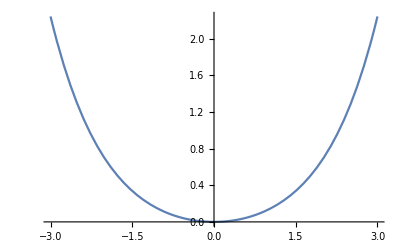

```mathematica
Plot[BesselI[2,x],{x,-3,3}]
```

```mathematica
CFunc = Exp[-alpha (r^2+ri^2)]Exp[-alpha (r^2+rj^2)]BesselI[l,2*alpha*r*ri]//FullSimplify
```

ⅇ^(-alpha (2 r^2+ri^2+rj^2)) BesselI[l,2 alpha r ri]

```mathematica
Integrate[CFunc,{r,0,Infinity}, Assumptions->{r>0,ri>0,rb>0,alpha>0,l>0}]
```

(ⅇ^(-alpha ((3 ri^2)/4+rj^2)) √(π/2) BesselI[l/2,(alpha ri^2)/4])/(2 √alpha)

```mathematica
AtomOverlap =(1/r) Exp[-a r^2]BesselI[l,b r]BesselI[l,c r]//FullSimplify
```

(ⅇ^(-a r^2) BesselI[l,b r] BesselI[l,c r])/r

```mathematica
Integrate[AtomOverlap,{r,0,Infinity}]
```

∫_0^∞ (ⅇ^(-a r^2) BesselI[l,b r] BesselI[l,c r])/r ⅆr

```mathematica
SphFunc = Exp[-alpha (r^2+ri^2)]Exp[-alpha (r-rj)]BesselI[l,2*alpha*r*ri]//FullSimplify
```

```mathematica
Integrate[BesselI[nu, b*t]*Exp[-p^2 (t-a)^2],{t,0,Infinity}]
```

∫_0^∞ ⅇ^(-p^2 (-a+t)^2) BesselI[nu,b t]ⅆt

```mathematica
Integrate[t^(nu+1) BesselI[nu, b*t]*Exp[-p^2 t^2],{t,0,Infinity}]
```

ConditionalExpression[2^(-1-nu) b^nu ⅇ^(b^2/(4 p^2)) (p^2)^(-1-nu),Re[b]≥0&&(Im[b]>0||Re[b]>0)&&Re[nu]>-1&&Re[p^2]>0]